## Aplicación de EigenValores-EigenVectores

```mathematica
m={{"Manzanas","peso(gr)","Volumen (cm^3)"},{m1,68.0,172.06},{m2,22.7,40.82},{m3,81.6,139.27},{m4,45.4,90.12},{m5,113,217.37},{m6,159,312.60},{m7,181,248.40},{m8,99.8,188.90}};
```

```mathematica
m//Dimensions
```

{9,3}

```mathematica
Grid[m[[1;;9,1;;3]],Frame->All,ItemSize->Automatic,Background->{None,{{LightBlue,LightGray}}}]
```

Manzanas | peso(gr) | Volumen (cm^3)
m1 | 68. | 172.06
m2 | 22.7 | 40.82
m3 | 81.6 | 139.27
m4 | 45.4 | 90.12
m5 | 113 | 217.37
m6 | 159 | 312.6
m7 | 181 | 248.4
m8 | 99.8 | 188.9

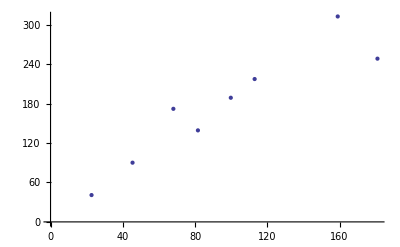

```mathematica
ListPlot[m[[2;;9,2;;3]]]
```

## Análisis de Componentes Principales (Básico)

### Matriz de Covarianza

```mathematica
m[[2;;9,2;;3]]//MatrixForm
```

(68. | 172.06
22.7 | 40.82
81.6 | 139.27
45.4 | 90.12
113 | 217.37
159 | 312.6
181 | 248.4
99.8 | 188.9)

### Calculando medias

```mathematica
mediaPeso=(∑_(i=2)^9 m[[i,2]])/8;
```

```mathematica
mediaVolumen=(∑_(i=2)^9 m[[i,3]])/8;
```

### Generando matriz de covarianza

```mathematica
Y=Table[{m[[i,2]]-mediaPeso,m[[i,3]]-mediaVolumen},{i,2,Length[m]}];
```

```mathematica
Y//MatrixForm
```

(-28.3125 | -4.1325
-73.6125 | -135.373
-14.7125 | -36.9225
-50.9125 | -86.0725
16.6875 | 41.1775
62.6875 | 136.408
84.6875 | 72.2075
3.4875 | 12.7075)

```mathematica
c=Transpose[Y].Y;
```

```mathematica
c//MatrixForm
```

(20421.3 | 30405.1
30405.1 | 52792.5)

### EigenValores y EigenVectores

```mathematica
Eigensystem[c]
```

```mathematica
(** Los dos primeros valores  son Eigenvalores, en el segundo grupo, hay 2 Eigenvectores. El Eigenvalor que tenga mayor peso (tamaño) corresponde al vector que proporciona a la exactitud **)
```

{{71051.7,2162.11},{{0.51483,0.857292},{-0.857292,0.51483}}}

```mathematica
f[x_]:=0.8572924548366432/0.5148297261038471 x;
```

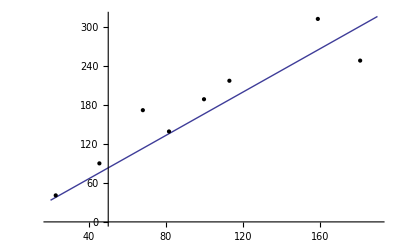

```mathematica
Plot[f[x],{x,20,190},Epilog->Map[Point,m[[2;;9,2;;3]]]]
```

```mathematica
m[[2;;9,2;;3]]
```

{{68.,172.06},{22.7,40.82},{81.6,139.27},{45.4,90.12},{113,217.37},{159,312.6},{181,248.4},{99.8,188.9}}

```mathematica
TableForm[Table[{m[[i,2]],m[[i,3]],f[m[[i,2]]]},{i,2,9}],TableHeadings->{None, {"Peso","Volumen","Pronóstico de Volumen"}}]
```

Peso | Volumen | Pronóstico de Volumen
68. | 172.06 | 113.233
22.7 | 40.82 | 37.8
81.6 | 139.27 | 135.88
45.4 | 90.12 | 75.5999
113 | 217.37 | 188.167
159 | 312.6 | 264.766
181 | 248.4 | 301.4
99.8 | 188.9 | 166.187